```mathematica
foo=Import["D:\\Dokumente\\Dissertation\\Code\\python\\ptsne-pytorch\\projected_output_test.csv", "Table"];
```

```mathematica
data=Partition[foo,60000];
```

```mathematica
vectors=Thread[{data⟦3⟧,data⟦4⟧}];
```

```mathematica
Graphics[{Opacity[0.3],Arrowheads[0.02],Arrow/@vectors⟦;;2000⟧},ImageSize->1500]
```

```mathematica
x1=data⟦1⟧;
x2=data⟦2⟧;
```

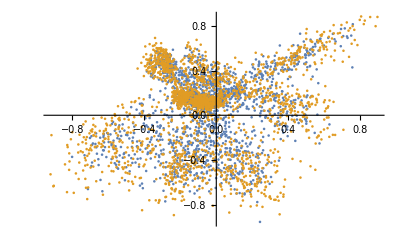

```mathematica
ListPlot[{RandomSample[x1n,2000],RandomSample[x2n,2000]}]
```

```mathematica
x1n=MapThread[Rescale,{x1ᵀ,MinMax/@(x2ᵀ),{{-1,1},{-1,1}}}]ᵀ;
```

```mathematica
x2n=MapThread[Rescale,{x2ᵀ,MinMax/@(x2ᵀ),{{-1,1},{-1,1}}}]ᵀ;
```

```mathematica
fn=x2n-x1n;
```

```mathematica
vectorsn=Thread[{x1n,x2n}];
```

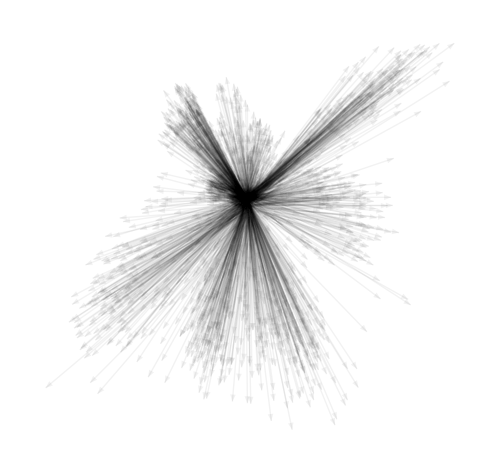

```mathematica
Graphics[{Opacity[0.05],Arrowheads[0.02],Arrow/@vectorsn⟦;;2000⟧},ImageSize->500]
```

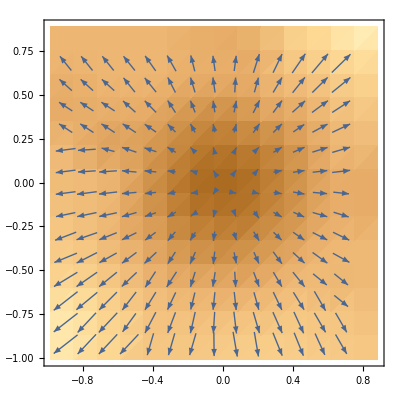

```mathematica
ListVectorDensityPlot[({x1n,x1n+fn}ᵀ)⟦;;5000⟧]
```

```mathematica
grid=Flatten[Table[{i,j},{i,-1,1,0.01},{j,-1,1,0.01}],1];
```

```mathematica
gauss[x0_,x_,f_]:=
```

```mathematica
Simplify[PDF[BinormalDistribution[{0.1,0.1},0],{xx,yy}]]
```

15.9155 ⅇ^(-50. xx^2-50. yy^2)

```mathematica
ListVectorPlot
```

```mathematica
Rescale[z,{a,b},{c,d}]
```

-(-b c+a d)/(-a+b)+((-c+d) z)/(-a+b)